```mathematica
(* 地球的轨道参数 *)
a=(152097701+147098074)/2;
e=0.0167086;
c=a*e;
b=√(a^2-c^2);
(* 月球的轨道参数 *)
am=(405696+363104)/2;
em=0.0549;
cm=am*em;
bm=√(am^2-cm^2);
```

```mathematica
f=365.256363004/27.321661
```

13.3687

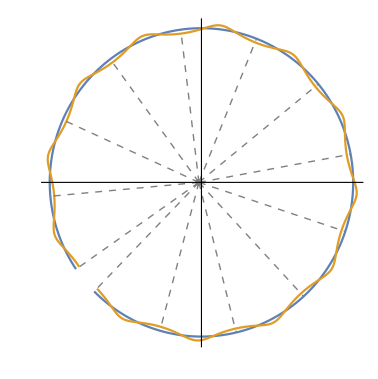

```mathematica
sun={-e*a,0};
δ=0.08;
η=-0.75π;
θ=(2π)/(f -1);
Show[
ParametricPlot[{{a Cos[t],b Sin[t]},{a Cos[t]+10*am Cos[-(f-2)(t+δ)],b Sin[t]+10*bm Sin[-(f-2) (t+δ)]}},{t,-0.75π,1.19π},Ticks->None],
ListPlot[{sun}],
ListLinePlot[Table[{sun,{a Cos[n θ+η],b Sin[n θ+η]}},{n,0,12}],PlotStyle->{{Gray,Dashed,Thin}}]
]
```

2015/07/07 地球过远日点，这天是农历五月廿二
2016/01/03 地球过近日点，这天是农历冬月廿四